# MMA数据保存

## 1. MMA数据导出保存

类似于MAtlab的.mat文件，我想要保存MMA的运行结果，方便下次使用。

参考：https://jingyan.baidu.com/article/414eccf6adde9c6b431f0aac.html

一般序列化（纯文本）是不能保存所有数据，那么就应该二进制存储。还好Mathematica提供一种二进制数据交换格式WDX, 可以将内核中的形态各异的数据原封不动的存到文件里。

Export导出WDX的基本用法

1. Export[“文件路径/文件名.wdx”, 待存储符号, ”WDX”]

Import导入WDX的基本用法

1. 待读取符号=Import[“文件路径/文件名.wdx”, ”WDX”];

### 1.1 创建非文本对象

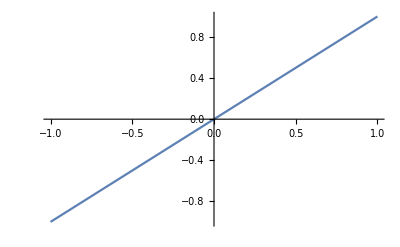

```mathematica
test = Plot[x, {x, -1, 1}]
```

```mathematica
test//Head
```

Graphics

### 1.2 保存这个符号

```mathematica
Export["C:\\Program Files\\Mathematica13\\Project\\Mathematica系统学习\\变量的保存\\fp.wdx", test, "WDX"]
```

C:\Program Files\Mathematica13\Project\Mathematica系统学习\变量的保存\fp.wdx

此时在这个路径下就产生了一个变量文件

	-Graphics-

### 1.3 测试导入

```mathematica
test
```

-Graphics-

```mathematica
Clear[test]
test
```

test

```mathematica
testimport = Import["C:\\Program Files\\Mathematica13\\Project\\Mathematica系统学习\\变量的保存\\fp.wdx", "WDX"];
```

```mathematica
testimport
```

-Graphics-

### 1.4 成功